```mathematica
19
```

## My 2HDM

### FeynRules Input

#### Be sure to quit the kernel before continuing Here we initialise FeynRules, set our directories, and load our *.fr model If you get red text “warnings”, you perhaps did not quit the kernel. Try again.

```mathematica
$FeynRulesPath=SetDirectory["/Users/laramason/Downloads/feynrules-current"];
<<FeynRules`;
SetDirectory[$FeynRulesPath<>"/Models/2HDM_add_vevs"];
FR$Parallelize = False;

LoadModel["2HDM.fr"];
FeynmanGauge = False;
(*LoadRestriction["Cabibbo.rst", "Massless.rst"]*)
(*WriteUFO[L2HDM, Output->"2HDM_UFO_Unitary"];*)
```

- FeynRules -

Version: 2.3.32 ( 12 March 2018).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

This model implementation was created by

C. Duhr

M. Herquet

C. Degrande

L. Mason

Model Version: 1.2

http://feynrules.phys.ucl.ac.be/view/Main/2HDM

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model 2HDM loaded.

Now we check the validity of the model

```mathematica
CheckHermiticity[L2HDM, FlavorExpand->True]
```

Checking for hermiticity by calculating the Feynman rules contained in L-HC[L].

If the lagrangian is hermitian, then the number of vertices should be zero.

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

No vertices found.

0 vertices obtained.

The lagrangian is hermitian.

{}

```mathematica
CheckDiagonalMassTerms[L2HDM]
```

Neglecting all terms with more than 2 particles.

Non diagonal mass term found: c_α^2 h1 h2 mu3+c_α h1 h2 mu1 s_α-c_α h1 h2 mu2 s_α-h1 h2 mu3 s_α^2+1.5 c_α h1 h2 λ_1 s_α vev1^2-1/2 c_α h1 h2 λ_4 s_α vev1^2-0.5 c_α h1 h2 λ_5 s_α vev1^2-c_α^2 h1 h2 λ_4 vev1 vev2-1. c_α^2 h1 h2 λ_5 vev1 vev2+h1 h2 λ_4 s_α^2 vev1 vev2+1. h1 h2 λ_5 s_α^2 vev1 vev2-1.5 c_α h1 h2 λ_2 s_α vev2^2+1/2 c_α h1 h2 λ_4 s_α vev2^2+0.5 c_α h1 h2 λ_5 s_α vev2^2

Non diagonal mass term found: -1/2 c_α h1 l vev1^2 vev2+1/2 h1 l s_α vev1 vev2^2

Non diagonal mass term found: -1/2 h2 l s_α vev1^2 vev2-1/2 c_α h2 l vev1 vev2^2

Non diagonal mass term found: -(vev2 (Γ_U)_(3,2)^* (c^-)_(r$3576,cc).t_(r$3577,cc) (P_-)_(r$3576,r$3577))/(√2)-(vev2 (c^-)_(sp2$3561,cc).t_(sp2$3558,cc) Γ_U_(2,3) (P_+)_(sp2$3561,sp2$3558))/(√2)

Non diagonal mass term found: -(vev2 (Γ_U)_(1,2)^* (c^-)_(r$3576,cc).u_(r$3577,cc) (P_-)_(r$3576,r$3577))/(√2)-(vev2 (c^-)_(sp2$3561,cc).u_(sp2$3558,cc) Γ_U_(2,1) (P_+)_(sp2$3561,sp2$3558))/(√2)

Non diagonal mass term found: -(vev2 (Γ_U)_(2,3)^* (t^-)_(r$3576,cc).c_(r$3577,cc) (P_-)_(r$3576,r$3577))/(√2)-(vev2 (t^-)_(sp2$3561,cc).c_(sp2$3558,cc) Γ_U_(3,2) (P_+)_(sp2$3561,sp2$3558))/(√2)

Non diagonal mass term found: -(vev2 (Γ_U)_(1,3)^* (t^-)_(r$3576,cc).u_(r$3577,cc) (P_-)_(r$3576,r$3577))/(√2)-(vev2 (t^-)_(sp2$3561,cc).u_(sp2$3558,cc) Γ_U_(3,1) (P_+)_(sp2$3561,sp2$3558))/(√2)

Non diagonal mass term found: -(vev2 (Γ_U)_(2,1)^* (u^-)_(r$3576,cc).c_(r$3577,cc) (P_-)_(r$3576,r$3577))/(√2)-(vev2 (u^-)_(sp2$3561,cc).c_(sp2$3558,cc) Γ_U_(1,2) (P_+)_(sp2$3561,sp2$3558))/(√2)

Non diagonal mass term found: -(vev2 (Γ_U)_(3,1)^* (u^-)_(r$3576,cc).t_(r$3577,cc) (P_-)_(r$3576,r$3577))/(√2)-(vev2 (u^-)_(sp2$3561,cc).t_(sp2$3558,cc) Γ_U_(1,3) (P_+)_(sp2$3561,sp2$3558))/(√2)

Non diagonal mass term found: -(vev2 (Γ_D)_(1,3)^* (b^-)_(r$3590,cc).d_(r$3591,cc) (P_-)_(r$3590,r$3591))/(√2)-(vev2 (b^-)_(sp2$3563,cc).d_(sp2$3557,cc) Γ_D_(3,1) (P_+)_(sp2$3563,sp2$3557))/(√2)

Non diagonal mass term found: -(vev2 (Γ_D)_(2,3)^* (b^-)_(r$3590,cc).s_(r$3591,cc) (P_-)_(r$3590,r$3591))/(√2)-(vev2 (b^-)_(sp2$3563,cc).s_(sp2$3557,cc) Γ_D_(3,2) (P_+)_(sp2$3563,sp2$3557))/(√2)

Non diagonal mass term found: -(vev2 (Γ_D)_(3,1)^* (d^-)_(r$3590,cc).b_(r$3591,cc) (P_-)_(r$3590,r$3591))/(√2)-(vev2 (d^-)_(sp2$3563,cc).b_(sp2$3557,cc) Γ_D_(1,3) (P_+)_(sp2$3563,sp2$3557))/(√2)

Non diagonal mass term found: -(vev2 (Γ_D)_(2,1)^* (d^-)_(r$3590,cc).s_(r$3591,cc) (P_-)_(r$3590,r$3591))/(√2)-(vev2 (d^-)_(sp2$3563,cc).s_(sp2$3557,cc) Γ_D_(1,2) (P_+)_(sp2$3563,sp2$3557))/(√2)

Non diagonal mass term found: -(vev2 (Γ_D)_(3,2)^* (s^-)_(r$3590,cc).b_(r$3591,cc) (P_-)_(r$3590,r$3591))/(√2)-(vev2 (s^-)_(sp2$3563,cc).b_(sp2$3557,cc) Γ_D_(2,3) (P_+)_(sp2$3563,sp2$3557))/(√2)

Non diagonal mass term found: -(vev2 (Γ_D)_(1,2)^* (s^-)_(r$3590,cc).d_(r$3591,cc) (P_-)_(r$3590,r$3591))/(√2)-(vev2 (s^-)_(sp2$3563,cc).d_(sp2$3557,cc) Γ_D_(2,1) (P_+)_(sp2$3563,sp2$3557))/(√2)

False

```mathematica
CheckMassSpectrum[L2HDM]
```

Neglecting all terms with more than 2 particles.

All mass terms are diagonal.

Warning: mass term for {A, A}seems not to have the correct sign.

Getting mass spectrum.

Checking for less then 0.1% agreement with model file values.

Particle | Analytic value | Numerical value | Model-file value
Hc | √(mu2+(λ_3 vev^2)/2) | 150. | 150.
b | (vev (y^d)_(3,3)^*)/(2 √2)+(vev (y^d)_(3,3))/(2 √2) | 4.7 | 4.7
d | (vev (y^d)_(1,1)^*)/(2 √2)+(vev (y^d)_(1,1))/(2 √2) | 0.00504 | 0.00504
s | (vev (y^d)_(2,2)^*)/(2 √2)+(vev (y^d)_(2,2))/(2 √2) | 0.101 | 0.101
e | (vev (y^l)_(1,1)^*)/(2 √2)+(vev (y^l)_(1,1))/(2 √2) | 0.000511 | 0.000511
mu | (vev (y^l)_(2,2)^*)/(2 √2)+(vev (y^l)_(2,2))/(2 √2) | 0.10566 | 0.10566
ta | (vev (y^l)_(3,3)^*)/(2 √2)+(vev (y^l)_(3,3))/(2 √2) | 1.777 | 1.777
c | (vev (y^u)_(2,2)^*)/(2 √2)+(vev (y^u)_(2,2))/(2 √2) | 1.27 | 1.27
t | (vev (y^u)_(3,3)^*)/(2 √2)+(vev (y^u)_(3,3))/(2 √2) | 172. | 172.
u | (vev (y^u)_(1,1)^*)/(2 √2)+(vev (y^u)_(1,1))/(2 √2) | 0.00255 | 0.00255
h1 | √2 √(1/2 mu1 (T_H)_(1,1)^2+3/2 λ_1 vev^2 (T_H)_(1,1)^2+1/2 mu3 T_H_(1,1) T_H_(2,1)+3/4 λ_6 vev^2 T_H_(1,1) T_H_(2,1)+3/4 vev^2 λ_6^* T_H_(1,1) T_H_(2,1)+1/2 mu3^* T_H_(1,1) T_H_(2,1)+1/2 mu2 (T_H)_(2,1)^2+1/4 λ_3 vev^2 (T_H)_(2,1)^2+1/4 λ_4 vev^2 (T_H)_(2,1)^2+1/4 λ_5 vev^2 (T_H)_(2,1)^2+1/4 vev^2 λ_5^* (T_H)_(2,1)^2+1/2 ⅈ mu3 T_H_(1,1) T_H_(3,1)+3/4 ⅈ λ_6 vev^2 T_H_(1,1) T_H_(3,1)-3/4 ⅈ vev^2 λ_6^* T_H_(1,1) T_H_(3,1)-1/2 ⅈ mu3^* T_H_(1,1) T_H_(3,1)+1/2 ⅈ λ_5 vev^2 T_H_(2,1) T_H_(3,1)-1/2 ⅈ vev^2 λ_5^* T_H_(2,1) T_H_(3,1)+1/2 mu2 (T_H)_(3,1)^2+1/4 λ_3 vev^2 (T_H)_(3,1)^2+1/4 λ_4 vev^2 (T_H)_(3,1)^2-1/4 λ_5 vev^2 (T_H)_(3,1)^2-1/4 vev^2 λ_5^* (T_H)_(3,1)^2) | 120. | 120.
h2 | √2 √(1/2 mu1 (T_H)_(1,2)^2+3/2 λ_1 vev^2 (T_H)_(1,2)^2+1/2 mu3 T_H_(1,2) T_H_(2,2)+3/4 λ_6 vev^2 T_H_(1,2) T_H_(2,2)+3/4 vev^2 λ_6^* T_H_(1,2) T_H_(2,2)+1/2 mu3^* T_H_(1,2) T_H_(2,2)+1/2 mu2 (T_H)_(2,2)^2+1/4 λ_3 vev^2 (T_H)_(2,2)^2+1/4 λ_4 vev^2 (T_H)_(2,2)^2+1/4 λ_5 vev^2 (T_H)_(2,2)^2+1/4 vev^2 λ_5^* (T_H)_(2,2)^2+1/2 ⅈ mu3 T_H_(1,2) T_H_(3,2)+3/4 ⅈ λ_6 vev^2 T_H_(1,2) T_H_(3,2)-3/4 ⅈ vev^2 λ_6^* T_H_(1,2) T_H_(3,2)-1/2 ⅈ mu3^* T_H_(1,2) T_H_(3,2)+1/2 ⅈ λ_5 vev^2 T_H_(2,2) T_H_(3,2)-1/2 ⅈ vev^2 λ_5^* T_H_(2,2) T_H_(3,2)+1/2 mu2 (T_H)_(3,2)^2+1/4 λ_3 vev^2 (T_H)_(3,2)^2+1/4 λ_4 vev^2 (T_H)_(3,2)^2-1/4 λ_5 vev^2 (T_H)_(3,2)^2-1/4 vev^2 λ_5^* (T_H)_(3,2)^2) | 130. | 130.
h3 | √2 √(1/2 mu1 (T_H)_(1,3)^2+3/2 λ_1 vev^2 (T_H)_(1,3)^2+1/2 mu3 T_H_(1,3) T_H_(2,3)+3/4 λ_6 vev^2 T_H_(1,3) T_H_(2,3)+3/4 vev^2 λ_6^* T_H_(1,3) T_H_(2,3)+1/2 mu3^* T_H_(1,3) T_H_(2,3)+1/2 mu2 (T_H)_(2,3)^2+1/4 λ_3 vev^2 (T_H)_(2,3)^2+1/4 λ_4 vev^2 (T_H)_(2,3)^2+1/4 λ_5 vev^2 (T_H)_(2,3)^2+1/4 vev^2 λ_5^* (T_H)_(2,3)^2+1/2 ⅈ mu3 T_H_(1,3) T_H_(3,3)+3/4 ⅈ λ_6 vev^2 T_H_(1,3) T_H_(3,3)-3/4 ⅈ vev^2 λ_6^* T_H_(1,3) T_H_(3,3)-1/2 ⅈ mu3^* T_H_(1,3) T_H_(3,3)+1/2 ⅈ λ_5 vev^2 T_H_(2,3) T_H_(3,3)-1/2 ⅈ vev^2 λ_5^* T_H_(2,3) T_H_(3,3)+1/2 mu2 (T_H)_(3,3)^2+1/4 λ_3 vev^2 (T_H)_(3,3)^2+1/4 λ_4 vev^2 (T_H)_(3,3)^2-1/4 λ_5 vev^2 (T_H)_(3,3)^2-1/4 vev^2 λ_5^* (T_H)_(3,3)^2) | 140. | 140.
W | 1/2 √(g_w^2 vev^2) | 79.8247 | 79.8247
Z | √2 √(1/8 c_w^2 g_w^2 vev^2+1/4 c_w g_1 g_w s_w vev^2+1/8 g_1^2 s_w^2 vev^2) | 91.1876 | 91.1876

```mathematica
CheckDiagonalKineticTerms[L2HDM]
```

All kinetic terms are diagonal.

True

```mathematica
CheckKineticTermNormalisation[L2HDM, FlavorExpand->True]
```

Neglecting all terms with more than 2 particles.

All kinetic terms are diagonal.

Warning: Kinetic term for {ve, vebar} seems not to be correctly normalized.

Warning: Kinetic term for {vm, vmbar} seems not to be correctly normalized.

Warning: Kinetic term for {vt, vtbar} seems not to be correctly normalized.

#### Generate FeynRules Output UFO

```mathematica
WriteUFO[L2HDM, Output->"2HDM_UFO_Unitary"];
```

--- Universal FeynRules Output (UFO) v 1.1 ---

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

71 possible non-zero vertices have been found -> starting the computation:  / 71.

57 vertices obtained.

Flavor expansion of the vertices:  / 57

- Saved vertices in InterfaceRun[ 1 ].

Computing the squared matrix elements relevant for the 1->2 decays:

/ 192

Squared matrix elent compute in 9.72686 seconds.

Decay widths computed in 0.167754 seconds.

Preparing Python output.

- Splitting vertices into building blocks.

- Optimizing: /281 .

- Writing files.

Done!

#### Generate Feynman Rules

```mathematica
(*verts2HDM = FeynmanRules[L2HDM]*)
(*verts2HDM = FlavourExpansion[ verts2HDM ]*)
vertsG=SelectVertices[verts2HDM,SelectParticles->{{G,G,G},{G,G,G,G}}]
(*decays = ComputeWidths[ verts2HDM ] *)
```

Applying seclection rules...

{{{{G,1},{G,2},{G,3}},g_s f_(a_1,a_2,a_3) p_1^μ_3 η_(μ_1,μ_2)-g_s f_(a_1,a_2,a_3) p_2^μ_3 η_(μ_1,μ_2)-g_s f_(a_1,a_2,a_3) p_1^μ_2 η_(μ_1,μ_3)+g_s f_(a_1,a_2,a_3) p_3^μ_2 η_(μ_1,μ_3)+g_s f_(a_1,a_2,a_3) p_2^μ_1 η_(μ_2,μ_3)-g_s f_(a_1,a_2,a_3) p_3^μ_1 η_(μ_2,μ_3)},{{{G,1},{G,2},{G,3},{G,4}},ⅈ g_s^2 f_(a_1,a_3,Gluon$1) f_(a_2,a_4,Gluon$1) η_(μ_1,μ_4) η_(μ_2,μ_3)+ⅈ g_s^2 f_(a_1,a_2,Gluon$1) f_(a_3,a_4,Gluon$1) η_(μ_1,μ_4) η_(μ_2,μ_3)+ⅈ g_s^2 f_(a_1,a_4,Gluon$1) f_(a_2,a_3,Gluon$1) η_(μ_1,μ_3) η_(μ_2,μ_4)-ⅈ g_s^2 f_(a_1,a_2,Gluon$1) f_(a_3,a_4,Gluon$1) η_(μ_1,μ_3) η_(μ_2,μ_4)-ⅈ g_s^2 f_(a_1,a_4,Gluon$1) f_(a_2,a_3,Gluon$1) η_(μ_1,μ_2) η_(μ_3,μ_4)-ⅈ g_s^2 f_(a_1,a_3,Gluon$1) f_(a_2,a_4,Gluon$1) η_(μ_1,μ_2) η_(μ_3,μ_4)}}

Now we generate the input for FeynArts

```mathematica
WriteFeynArtsOutput[L2HDM, FlavorExpand->SU2W]
```

- - - FeynRules interface to FeynArts - - -

C. Degrande C. Duhr, 2013

Counterterms: B. Fuks, 2012

Creating output directory: 2HDM_FA

Calculating Feynman rules for L1

Starting Feynman rules calculation for L1.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

71 possible non-zero vertices have been found -> starting the computation:  / 71.

57 vertices obtained.

Simplify::time: Time spent on a transformation exceeded 0.01 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

Writing FeynArts model file into directory 2HDM_FA

Writing FeynArts generic file on 2HDM_FA.gen.

Initialise FeynArts, FormCalc

Be sure to quit the Kernel before continuing

```mathematica
<<FeynArts`
<< FormCalc`
model=FileNameJoin[{NotebookDirectory[],"2HDM_FA","2HDM_FA"}];
(*_Hel=0;*)
```

FeynArts 3.10 (21 Jan 2019)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

Check that the model files exist

```mathematica
FileExistsQ[model<>".mod"]
FileExistsQ[model<>".gen"]
```

True

True

Create Topologies

> Top. 1 aebe/cede/0.m, 1 diagram

> Top. 2 aebe/cfdf/ef.m, 1 diagram

> Top. 3 aebf/cedf/ef.m, 1 diagram

> Top. 4 aebf/cfde/ef.m, 1 diagram



```mathematica
topo=CreateTopologies[0,2->2];
Paint[topo];
```

Insert some fields: let’s start with inserting a scalar (H)

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 3 Classes insertions

> Top. 3: 3 Classes insertions

> Top. 4: 3 Classes insertions

in total: 10 Classes insertions

TopologyList[Process→{S[2,{Hig1}],S[2,{Hig2}]}→{S[2,{Hig3}],S[2,{Hig4}]},Model→{/Users/laramason/Downloads/feynrules-current/Models/2HDM_Lara/2HDM_FA/2HDM_FA},GenericModel→{/Users/laramason/Downloads/feynrules-current/Models/2HDM_Lara/2HDM_FA/2HDM_FA},InsertionLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[4][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5],Field[4]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→S[2,{Hig1}],Field[2]→S[2,{Hig2}],Field[3]→S[2,{Hig3}],Field[4]→S[2,{Hig4}]]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→S[2,{Hig1}],Field[2]→S[2,{Hig2}],Field[3]→S[2,{Hig3}],Field[4]→S[2,{Hig4}]]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→S[2,{Hig1}],Field[2]→S[2,{Hig2}],Field[3]→S[2,{Hig3}],Field[4]→S[2,{Hig4}],Field[5]→S]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→S[2,{Hig1}],Field[2]→S[2,{Hig2}],Field[3]→S[2,{Hig3}],Field[4]→S[2,{Hig4}],Field[5]→S[2,{Hig5}]]],FeynmanGraph[1,Generic==2][Field[1]→S[2,{Hig1}],Field[2]→S[2,{Hig2}],Field[3]→S[2,{Hig3}],Field[4]→S[2,{Hig4}],Field[5]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→S[2,{Hig1}],Field[2]→S[2,{Hig2}],Field[3]→S[2,{Hig3}],Field[4]→S[2,{Hig4}],Field[5]→V[1]],FeynmanGraph[1,Classes==2][Field[1]→S[2,{Hig1}],Field[2]→S[2,{Hig2}],Field[3]→S[2,{Hig3}],Field[4]→S[2,{Hig4}],Field[5]→V[2]]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→S[2,{Hig1}],Field[2]→S[2,{Hig2}],Field[3]→S[2,{Hig3}],Field[4]→S[2,{Hig4}],Field[5]→S]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→S[2,{Hig1}],Field[2]→S[2,{Hig2}],Field[3]→S[2,{Hig3}],Field[4]→S[2,{Hig4}],Field[5]→S[2,{Hig5}]]],FeynmanGraph[1,Generic==2][Field[1]→S[2,{Hig1}],Field[2]→S[2,{Hig2}],Field[3]→S[2,{Hig3}],Field[4]→S[2,{Hig4}],Field[5]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→S[2,{Hig1}],Field[2]→S[2,{Hig2}],Field[3]→S[2,{Hig3}],Field[4]→S[2,{Hig4}],Field[5]→V[1]],FeynmanGraph[1,Classes==2][Field[1]→S[2,{Hig1}],Field[2]→S[2,{Hig2}],Field[3]→S[2,{Hig3}],Field[4]→S[2,{Hig4}],Field[5]→V[2]]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][6],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→S[2,{Hig1}],Field[2]→S[2,{Hig2}],Field[3]→S[2,{Hig3}],Field[4]→S[2,{Hig4}],Field[5]→S]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→S[2,{Hig1}],Field[2]→S[2,{Hig2}],Field[3]→S[2,{Hig3}],Field[4]→S[2,{Hig4}],Field[5]→S[2,{Hig5}]]],FeynmanGraph[1,Generic==2][Field[1]→S[2,{Hig1}],Field[2]→S[2,{Hig2}],Field[3]→S[2,{Hig3}],Field[4]→S[2,{Hig4}],Field[5]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→S[2,{Hig1}],Field[2]→S[2,{Hig2}],Field[3]→S[2,{Hig3}],Field[4]→S[2,{Hig4}],Field[5]→V[1]],FeynmanGraph[1,Classes==2][Field[1]→S[2,{Hig1}],Field[2]→S[2,{Hig2}],Field[3]→S[2,{Hig3}],Field[4]→S[2,{Hig4}],Field[5]→V[2]]]]]

> Top. 1 aebe/cede/0.m, 1 diagram

> Top. 2 aebe/cfdf/ef.m, 3 diagrams

> Top. 3 aebf/cedf/ef.m, 3 diagrams

> Top. 4 aebf/cfde/ef.m, 3 diagrams

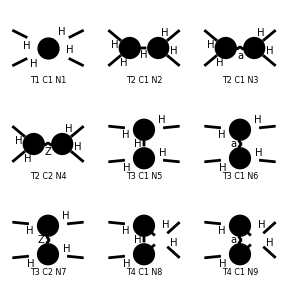

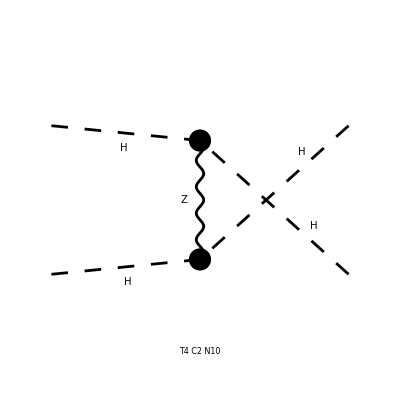

```mathematica
diag=InsertFields[topo,{S[2],S[2]}->{S[2],S[2]},InsertionLevel->{Classes},
Model->model,GenericModel->model]
Paint[diag];
```

Calculate Amplitude

```mathematica
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA]
SquaredME[amp]
%[[1]]//.%[[2]]
%//FullForm
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 3 Classes amplitudes

> Top. 3: 3 Classes amplitudes

in total: 7 Classes amplitudes

preparing FORM code in /Users/laramason/fc-amp-1.frm

running FORM...

ReadForm::formerror: \!\(\*RowBox[{"\"MH has been declared as a symbol \\nIllegal use of function arguments\\nInternal error in code generator.\""}]\)

$Aborted

SquaredME[amp,amp]

ReplaceRepeated::reps: \!\(\*RowBox[{"{", "amp", "}"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

amp//.amp

ReplaceRepeated[amp,amp]